```mathematica
Clear["*"];
```

```mathematica
$DisplayFunction=Identity;
```

```mathematica
Kx=1;Ky=1;Kz=0;Kd=-{1,10,100};
```

```mathematica
ω0=2 Pi/360000;
```

```mathematica
ωinit={.3,.5,.4}; qinit={.5,.5,.5,.5};
```

```mathematica
Bo[t_]:=10^(-4) {Sin[ω0 t],Cos[ω0 t],0};
```

```mathematica
Bdoto[t_]:=Bo'[t];
```

```mathematica
Ix=1;Iy=2;Iz=3;
```

```mathematica
n=3.2;
```

```mathematica
P[v_]:=0.5*Table[{{0, v[[3]],-v[[2]], v[[1]]},{-v[[3]], 0, v[[1]], v[[2]]},{v[[2]],-v[[1]], 0, v[[3]]},{-v[[1]],-v[[2]],-v[[3]], 0}}]
```

```mathematica
skewsym[v_]:=Table[{{0, v[[3]],-v[[2]]},{-v[[3]], 0, v[[1]]},{v[[2]],-v[[1]], 0}}]
```

```mathematica
Isat=Table[{{Ix,0,0},{0,Iy,0},{0,0,Iz}}];
```

```mathematica
σ1=(Iy-Iz)/Ix; σ2=(Iz-Ix)/Iy;σ3=(Ix-Iy)/Iz;
```

```mathematica
quaternioninverse[q_]:={-q[[1]],-q[[2]],-q[[3]],q[[4]]}
```

```mathematica
quaternionmultiply[q1_,q2_]:={q1[[4]] q2[[4]]-q1[[1]] q2[[1]]-q1[[2]] q2[[2]]-q1[[3]] q2[[3]],q1[[3]] q2[[2]]-q1[[2]] q2[[3]],q1[[1]] q2[[3]]-q1[[3]] q2[[1]],q1[[2]] q2[[1]]-q1[[1]] q2[[2]]}
```

```mathematica
quaternionrotate[q_,v_]:={{1-2q[[2]]^2-2q[[3]]^2,2(q[[1]] q[[2]]+q[[4]] q[[3]]),2(q[[1]] q[[3]]-q[[4]] q[[2]])},{2(q[[1]] q[[2]]-q[[4]] q[[3]]),1-2q[[1]]^2-2q[[3]]^2,2(q[[2]] q[[3]]+q[[4]] q[[1]])},{2(q[[1]] q[[3]]+q[[4]] q[[2]]),2(q[[2]] q[[3]]-q[[4]] q[[1]]),1-2q[[1]]^2-2q[[2]]^2}}.v
```

```mathematica
τc[q_,qreq_,ω_]:=(
qe={{qreq[[4]],qreq[[3]],-qreq[[2]],qreq[[1]]},{-qreq[[3]],qreq[[4]],qreq[[1]],qreq[[2]]},{qreq[[2]],-qreq[[1]],qreq[[4]],qreq[[3]]},{-qreq[[1]],-qreq[[2]],-qreq[[3]],qreq[[4]]}}.quaternioninverse[q];
Table[2 Kx qe[[i]] qe[[4]]+Kd[[i]] ω[[i]],{i,1,3}])
```

```mathematica
QuaternionDerivative[x_,ω_]:=P[ω].x
```

```mathematica
AngVelDerivative[ω_,τ_]:=Inverse[Isat].τ-{σ1 ω[[2]] ω[[3]],σ2 ω[[3]] ω[[1]],σ3 ω[[1]] ω[[2]]}
```

```mathematica
eqs3={Table[y[i]'[x]==QuaternionDerivative[Table[y[j][x],{j,1,4}],Table[y[i][x],{i,5,7}]-quaternionrotate[Table[y[i][x],{i,1,4}],{0,ω0,0}]][[i]],{i,1,4}],Table[y[i][0]== qinit[[i]],{i,1,4}],
Table[y[i]'[x]==AngVelDerivative[Table[y[j][x],{j,5,7}],τc[Table[y[i][x],{i,1,4}],{0,0,0,1},Table[y[i][x],{i,5,7}]]][[i-4]],{i,5,7}],Table[y[i][0]== ωinit[[i-4]],{i,5,7}]};
```

```mathematica
Needs["DifferentialEquations`NDsol2veProblems`"];
Needs["DifferentialEquations`NDsol2veUtilities`"];
Needs["FunctionApproximations`"];
```

```mathematica
sol3=NDSolve[eqs3,Table[y[i],{i,1,7}],{x,0,10^n}]
```

{{y[1]→InterpolatingFunction[{{0.,1584.89}},<>],y[2]→InterpolatingFunction[{{0.,1584.89}},<>],y[3]→InterpolatingFunction[{{0.,1584.89}},<>],y[4]→InterpolatingFunction[{{0.,1584.89}},<>],y[5]→InterpolatingFunction[{{0.,1584.89}},<>],y[6]→InterpolatingFunction[{{0.,1584.89}},<>],y[7]→InterpolatingFunction[{{0.,1584.89}},<>]}}

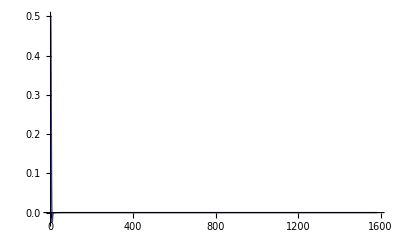

```mathematica
Plot[Evaluate[y[1][x]/.sol3,{x,0,10^n}],PlotRange->Full]
```

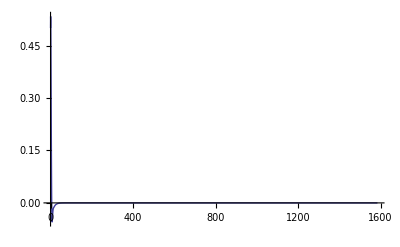

```mathematica
Plot[Evaluate[y[2][x]/.sol3,{x,0,10^n}],PlotRange->Full]
```

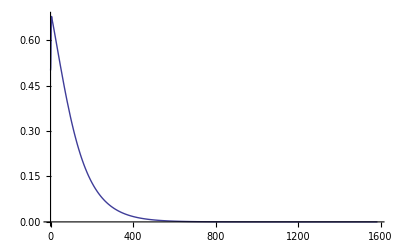

```mathematica
Plot[Evaluate[y[3][x]/.sol3,{x,0,10^n}],PlotRange->Full]
```

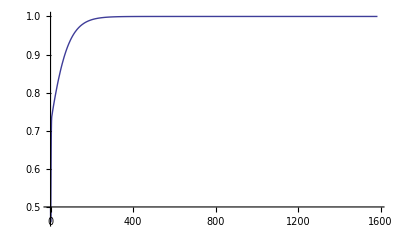

```mathematica
Plot[Evaluate[y[4][x]/.sol3,{x,0,10^n}],PlotRange->Full]
```

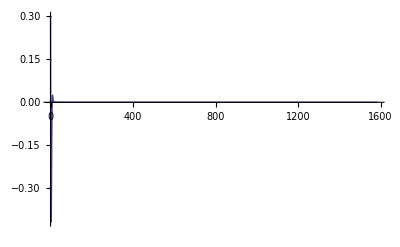

```mathematica
Plot[Evaluate[y[5][x]/.sol3,{x,0,10^n}],PlotRange->{Full,All}]
```

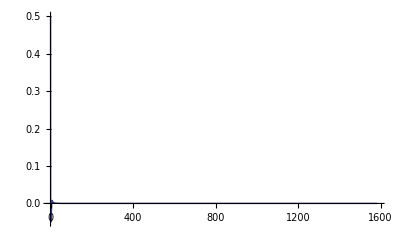

```mathematica
Plot[Evaluate[y[6][x]/.sol3,{x,0,10^n}],PlotRange->{Full,All}]
```

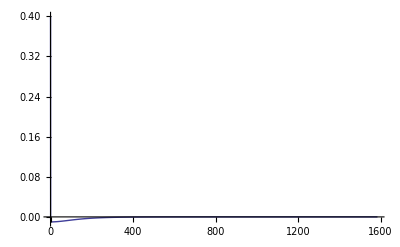

```mathematica
Plot[Evaluate[y[7][x]/.sol3,{x,0,10^n}],PlotRange->{Full,All}]
```